### Mathematica intro

#### basics

```mathematica
Plot[Sin[x]+Sin[1.6x],{x,0,40}]
```

```mathematica
Plot[{Sin[x], Sin[2x], Sin[3x]}, {x, 0, 2Pi},
PlotStyle->{Red,Blue,Black}]
```

```mathematica
Sin[0.99]
```

```mathematica
Plot3D[Sin[x y],{x,0,4},{y,0,4}]
```

```mathematica
LegendreQ[3,x]
```

```mathematica
Solve[x^2+x==a,x]
```

```mathematica
Integrate[Sqrt[x] Sqrt[1+x],x]
```

```mathematica
tmp2 = Table[RandomReal[],{500},{500}];
```

```mathematica
ArrayPlot[tmp2]
```

```mathematica
ListPlot[Abs[Eigenvalues[tmp2]]]
```

#### graphs

```mathematica
SeedRandom[6446]
```

```mathematica
RandomGraph[{20,40}]
```

#### Wolfram alpha

```mathematica
WolframAlpha["population of germany "]
```

```mathematica
WolframAlpha["population of germany ",{{"RecentHistory:Population:CountryData",1},"Content"}]
```

```mathematica
dataTemp1 = WolframAlpha["population of germany ",{{"RecentHistory:Population:CountryData",1},"TimeSeriesData"}]
```

```mathematica
WolframAlpha["human chromosome 1"]
```

```mathematica
WolframAlpha["human chromosome 1",{{"ChromosomeLength:GenomeSequenceData",1},"ComputableData"}]
```

```mathematica
tabLength = Append[Table[{"chr"<>ToString[k],WolframAlpha["human chromosome "<>ToString[k],{{"ChromosomeLength:GenomeSequenceData",1},"NumberData"}]*1000000},{k,1,21,1}],{"chrX",WolframAlpha["human chromosome X",{{"ChromosomeLength:GenomeSequenceData",1},"NumberData"}]*1000000}]
```

```mathematica
ListPlot[tabLength /. {n1_,n2_}-> n2,Frame->True,PlotStyle->{Black,AbsolutePointSize[5]},FrameTicks->{{Automatic,Automatic},{Thread[{Table[k,{k,1,Length[tabLength]}],tabLength /. {n1_,n2_}-> n1}],Automatic}},AspectRatio->0.2,ImageSize->700,FrameTicksStyle->Directive[Black,10,Plain],FrameLabel->{None,"Length"},LabelStyle->Directive[Black,14],Axes->False]
```

```mathematica
WolframAlpha["human chromosome 1 ideogram",{{"Result",1},"Content"}]
```

### logistic map

#### implementation

```mathematica
f[u_] := r u (1-u);
```

```mathematica
r = 3.75;
l1 = NestList[f,0.01,10]
Clear[r]
```

```mathematica
lp1 = ListPlot[l1,Frame->True,Joined->True]
```

```mathematica
lp1 = ListPlot[l1,Frame->True,Joined->True,PlotStyle->Blue];
lp2 = ListPlot[l1,Frame->True,PlotStyle-> {{AbsolutePointSize[8],Blue}}];
Show[lp1,lp2]
```

#### bifurcation diagram

```mathematica
bif1 = Table[{r,#}& /@ Take[NestList[f,0.01,500],-50],{r,0.5,4,0.01}];
```

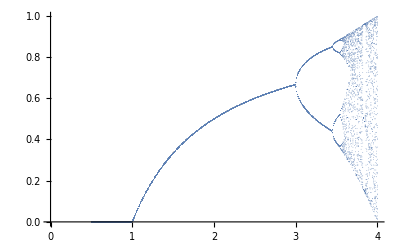

```mathematica
ListPlot[Flatten[bif1,1], PlotStyle->PointSize[0.001]]
```

```mathematica
bif1 = Table[{r,#}& /@ Take[NestList[f,0.01,500],-50],{r,0.5,4,0.001}];
ListPlot[Flatten[bif1,1], PlotStyle->PointSize[0.001]]
```

```mathematica
bif1 = Table[{r,#}& /@ Take[NestList[f,0.01,500],-50],{r,3.4,3.6,0.0001}];
ListPlot[Flatten[bif1,1], PlotStyle->PointSize[0.001],AspectRatio->1.5]
```

#### chaotic regime

```mathematica
r = 3.9;
l1 = NestList[f,0.09,50];
Clear[r]
ListPlot[l1,Frame->True,PlotStyle->{{AbsolutePointSize[7],Blue}},PlotRange->All,Joined->True,Mesh->All]
```

```mathematica
r = 3.9;
l1 = NestList[f,0.09,200];
Clear[r]
xx1 = ListPlot[l1,Frame->True,PlotStyle->{{AbsolutePointSize[7],Blue}},PlotRange->All,Joined->True,Mesh->All]
```

```mathematica
r = 3.9;
l1 = NestList[f,0.1,200];
Clear[r]
xx2 = ListPlot[l1,Frame->True,PlotStyle->{{AbsolutePointSize[7],Red}},PlotRange->All,Joined->True,Mesh->All]
```

```mathematica
Show[xx1,xx2,ImageSize->600]
```